## Battlecode Simulation v 4

## Simulation code

```mathematica
(*BASIC UTILITY FUNCTIONS*)
nextTurnResources[numberOfBots_, bytecodeUsage_, currentResources_, decayMultiplier_: .8] := Module[{},
   currentResources*decayMultiplier - numberOfBots*(1 + bytecodeUsage/10000) + 40
   ];
buildMoreBots[howOften_] := (
  If[(round - howOften >= lastBotBuiltRound) && round > 0, lastBotBuiltRound = round; numberOfBots = numberOfBots + 1];
  myResources[[round + 1]] = nextTurnResources[numberOfBots, bytecodeUsage, myResources[[round]], decayMultiplier];
  )
killExcessBots[] := If[myResources[[round + 1]] < 0, numberOfBots = numberOfBots - 1];
(*PLOTTING*)
plotResults[] := Module[{},
  plotOptions = {PlotRange -> All, AspectRatio -> 1/3, ImagePadding -> 20 {{1.5, 3}, {1, 1}}, ImageSize -> {600, 200}, PlotStyle -> Thick, BaseStyle -> {FontFamily -> "Calibri", FontSize -> 14}};
  generatorsAndSuppliers = ListPlot[{generators, suppliers}*{.8, .6}*Max@myResources, PlotStyle -> {Red, Black}];
  Return@{
    Show[ListLinePlot[myResources, plotOptions, AxesLabel -> {"Round", "Power"}], generatorsAndSuppliers]
    , ListLinePlot[botCount, plotOptions, AxesLabel -> {"Round", "# Robots"}]
    , Row[{Max@botCount
      , " Robots at round "
      , Position[botCount, Max@botCount][[1, 1]]
      , "."}, BaseStyle -> {FontFamily -> "Calibri", FontSize -> 14}]
    , ListLinePlot[Differences@Flatten@Position[Differences@botCount, 1], plotOptions[[2 ;;]], AxesLabel -> {"Round", "Spawn Time"}
     , PlotRange -> {Automatic, {0, 11}}]}
  ]

(*GENERATOR CODE*)
generatorBonus[round_,tryToBuild_]:= (
(*get additional resources from generators*)
myResources[[round]] = myResources[[round]]+10*generatorNumber;
If[(tryToBuild)
&&myResources[[round]]>10*(encampmentCount+1)+numberOfBots
&&round<(Length@generators-50)
&&numberOfBots-reservedBots>0
,
myResources[[round]]=myResources[[round]]-10*(encampmentCount+1);
generators[[round+50]]=1;
current++;(*advance build order*)
encampmentCount++;
reservedBots++;
];
generatorNumber = generatorNumber+generators[[round]];
numberOfBots= numberOfBots-generators[[round]];
reservedBots = reservedBots - generators[[round]];
)
(*SUPPLIER CODE*)
supplierBonus[round_,tryToBuild_]:= (
(*build encampments*)
If[(tryToBuild)
&&myResources[[round]]>10*(encampmentCount+1)+numberOfBots
&&round<(Length@generators-50)
&&numberOfBots-reservedBots>0
,
myResources[[round]]=myResources[[round]]-10*(encampmentCount+1);
suppliers[[round+50]]=1;
current++;(*advance build order*)
encampmentCount++;
reservedBots++;
];
supplierNumber= supplierNumber+suppliers[[round]];
numberOfBots= numberOfBots-suppliers[[round]];
reservedBots = reservedBots - suppliers[[round]];
spawnTime = 10*(10/(10+supplierNumber));
)
(*COMBINED MODEL*)
battlecodeModelExplicit[numRounds_,decayMultiplier_,bytecodeUsage_,buildOrderIn_]:= Module[{buildOrder = buildOrderIn},
myResources = ConstantArray[0,numRounds];
generators = ConstantArray[0,numRounds];
suppliers = ConstantArray[0,numRounds];
reservedBots = 0;
numberOfBots = 0;
generatorNumber = 0;
supplierNumber = 0;
encampmentCount = generatorNumber+supplierNumber;
spawnTime = 10;
lastBotBuiltRound = -1000;
current = 1;
botCount = Table[
buildGenerator =False;buildSupplier = False;
If[current≤ Length@buildOrder,
If[buildOrder[[current]]==1,buildGenerator = True];
If[buildOrder[[current]] ==2,buildSupplier = True];
If[buildOrder[[current]] ==0,current++];
If[buildOrder[[current]]<0,buildOrder[[current]]++];(*allows a delay to be specified as a negative number*)
];
generatorBonus[round,buildGenerator];
supplierBonus[round,buildSupplier];
buildMoreBots[spawnTime];
killExcessBots[];
numberOfBots
,{round,1,numRounds-1}];
Return@plotResults[]
]
```

## Usage

KEY: Generator is 1, Supplier is 2, a negative number is a pause.

Builds no encampments:

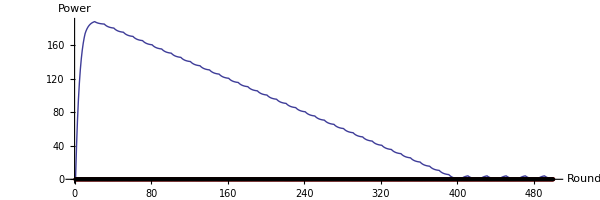
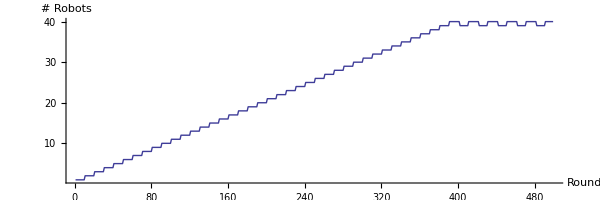
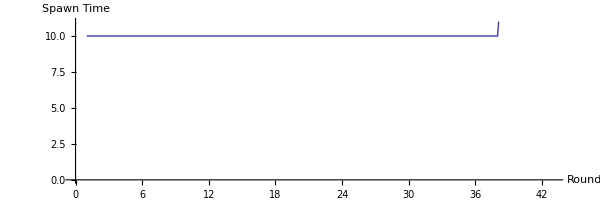
-Graphics-
-Graphics-
40 Robots at round 391.
-Graphics-

```mathematica
Column@battlecodeModelExplicit[
numberOfRounds = 500
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{}
]
```

Waits 50 rounds, then builds suppliers

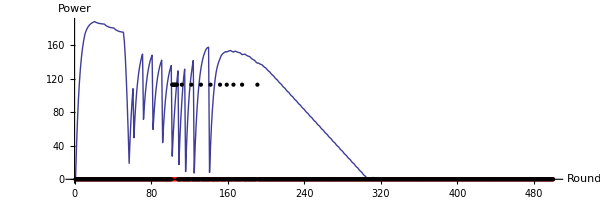
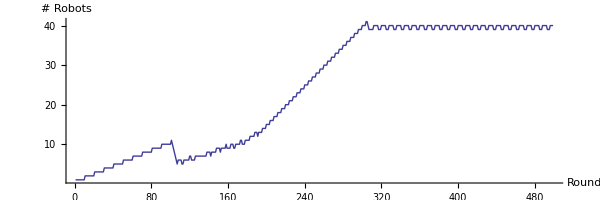
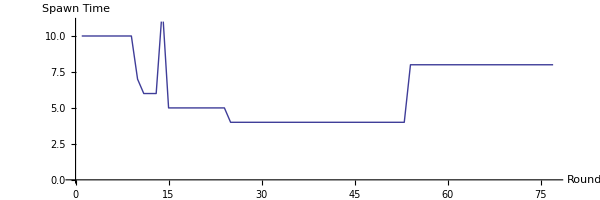
-Graphics-
-Graphics-
41 Robots at round 304.
-Graphics-

```mathematica
Column@battlecodeModelExplicit[
numberOfRounds = 500
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{-50,ConstantArray[2,100]}
]
```

Waits 50 rounds, then builds suppliers every 20 rounds

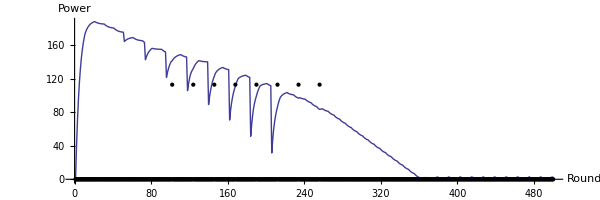
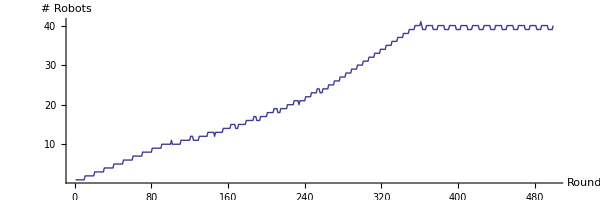
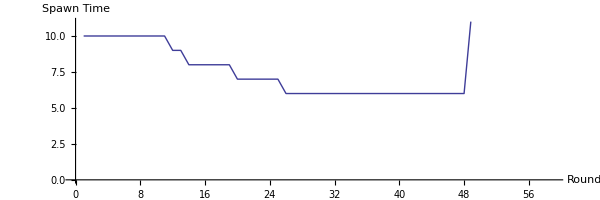
-Graphics-
-Graphics-
41 Robots at round 361.
-Graphics-

```mathematica
Column@battlecodeModelExplicit[
numberOfRounds = 500
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{-50,ConstantArray[{2,-20},100]}
]
```

Waits 50 rounds, then alternates suppliers and generators every 20 rounds

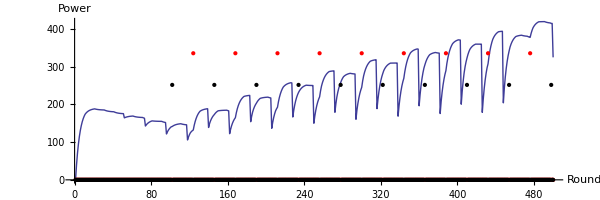
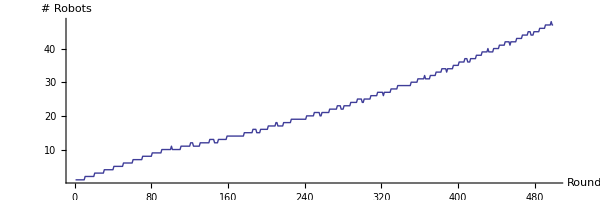
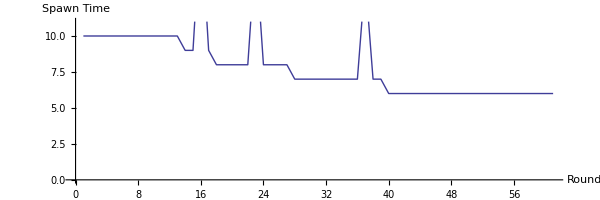
-Graphics-
-Graphics-
48 Robots at round 497.
-Graphics-

```mathematica
Column@battlecodeModelExplicit[
numberOfRounds = 500
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{-50,ConstantArray[{2,-20,1,-20},100]}
]
```

## Compare strategies intelligently:

KEY : Generator is 1, Supplier is 2, a negative number is a pause.

```mathematica
compareStrategies[strategyList_,numRnd_:500]:= Module[{},
{res,counts} = Transpose@Table[
battlecodeModelExplicit[
numberOfRounds = numRnd
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@strategyList[[i]]
];
{myResources,botCount}
,{i,1,Length@strategyList}];
]
```

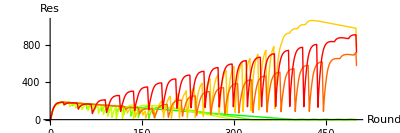
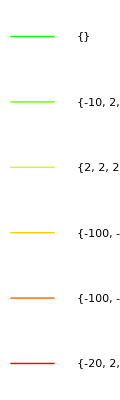
-Graphics--Graphics--Graphics-

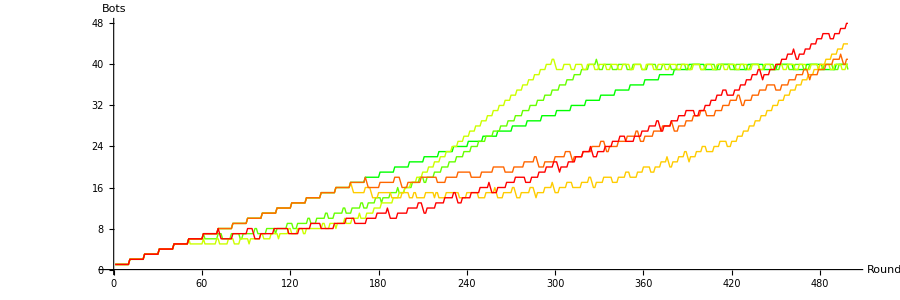

```mathematica
strategyList = {
{}
,{ConstantArray[{-10,2},20]}
,{ConstantArray[{2},20]}
,{-100,ConstantArray[{-10,2,1},20]}
,{-100,ConstantArray[{-20,2,1},20]}
,{ConstantArray[{-20,2,1},20]}
};
strategyNames = ToString@Flatten[#][[;;Min[Length@Flatten@#,10]]]&/@strategyList;
compareStrategies[strategyList,500]
opt = {BaseStyle-> {FontFamily-> "Calibri",14},AspectRatio->1/3,ImagePadding -> 20 {{1.5, 3}, {1, 1}},ImageSize-> {900,Automatic},PlotStyle-> 
Table[Directive[{RGBColor[2j,2-2j,0],Thick}],{j,0,1,1/(Length@strategyList-1)}]
};
Needs["maxLegend`","C:\\Users\\Max\\Dropbox\\backup\\mathematica projects\\maxLegend.m"]
formatLegend[ListLinePlot[res,opt,AxesLabel-> {"Round","Res"}],strategyNames]
ListLinePlot[counts,opt,AxesLabel-> {"Round","Bots"}]
```

# Encounters of units

## Let’s assume they all are dealing damage

The first units deal damage equally
the next ones deal damage to one unit, going along

```mathematica
team1Units = 10;(*make sure this number is less than team 2 units*)
team2Units = 10;
team1hp = ConstantArray[40,team1Units];
team2hp = ConstantArray[40,team2Units];
```

```mathematica
getNextHP[]:= (
team2hp[[;;team1Units]] = team2hp[[;;team1Units]]-6;
team1hp[[;;]] = team1hp[[;;]]-6;
remainingUnits = Min[team2Units-team1Units,team1Units];
team1hp[[;;remainingUnits]]= team1hp[[;;remainingUnits]]-6;
(*now reduce the number of units*)
team1hp = Select[team1hp,#>0&];
team1Units = Length@team1hp;
team2hp = Select[team2hp,#>0&];
team2Units = Length@team2hp;
)
```

```mathematica
simulateCombat[team1UnitsIn_,team2UnitsIn_]:= Module[{t},
team1Units = team1UnitsIn;
team2Units = team2UnitsIn;
(*team1Units = 10;(*make sure this number is less than team 2 units*)
team2Units = 11;*)
team1hp = ConstantArray[40,team1Units];
team2hp = ConstantArray[40,team2Units];
(*Print@Dynamic@team1hp;
Print@Dynamic@team2hp;*)
While[team1Units>0,
getNextHP[];
(*Pause[0];*)
];
unitKillRatio = team1UnitsIn/Max[(team2UnitsIn-team2Units),.001];
hpKillRatio = team1UnitsIn*40/Max[(team2UnitsIn*40-Total@team2hp),.001];
Return@{{"Robot Kill Ratio",N@unitKillRatio},{"HP Kill Ratio",N@hpKillRatio}}
]
```

```mathematica
TableForm@simulateCombat[10,11]
```

Robot Kill Ratio | 1.42857
HP Kill Ratio | 1.06383

# Let’s look at a lot of results

```mathematica
combatResults = Table[
Flatten[{N@i/20,simulateCombat[20,i][[;;,2]]}]
,{i,21,30}];
Style[TableForm[Join[{{"Force Ratio","Unit Kill Ratio","HP Kill Ratio"}},
combatResults
]],FontSize-> 14,FontFamily-> "Calibri"
]
```

Force Ratio | Unit Kill Ratio | HP Kill Ratio
1.05 | 1.17647 | 1.03093
1.1 | 1.42857 | 1.06383
1.15 | 1.81818 | 1.0989
1.2 | 2.5 | 1.13636
1.25 | 4. | 1.17647
1.3 | 10. | 1.21951
1.35 | 20000. | 1.25786
1.4 | 20000. | 1.28205
1.45 | 20000. | 1.30719
1.5 | 20000. | 1.33333

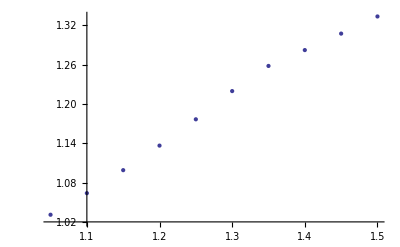

```mathematica
pts = ListPlot[combatResults[[;;,{1,3}]],PlotStyle-> Thick]
```

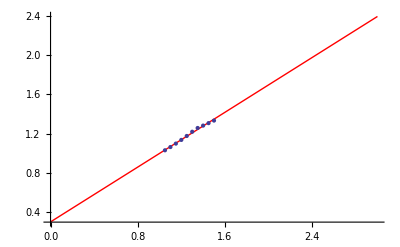

0.302247+0.696782 x

```mathematica
theline = a x + b/.FindFit[combatResults[[;;,{1,3}]],a x + b,{a,b},x];
Show[Plot[theline,{x,0,3},PlotStyle-> Red],pts]
theline
```

```mathematica
spawnTable = Table[
Join[{n},Round@{(10*.95^n),100/(10+n)}]
,{n,0,50}];
hpPerTurn = 40/spawnTable[[;;,3]];
incrementalBonus = Join[{0},Differences@hpPerTurn];
spawnTable= N@Join[spawnTable,List/@hpPerTurn,List/@incrementalBonus,2];
TableForm@Join[{{"# Suppp","Old Spec\n Spawn Delay","Latest Spec\n Spawn Delay","HP/round","+HP/round"}},spawnTable]
```

# Suppp | Old Spec
 Spawn Delay | Latest Spec
 Spawn Delay | HP/round | +HP/round
0. | 10. | 10. | 4. | 0.
1. | 10. | 9. | 4.44444 | 0.444444
2. | 9. | 8. | 5. | 0.555556
3. | 9. | 8. | 5. | 0.
4. | 8. | 7. | 5.71429 | 0.714286
5. | 8. | 7. | 5.71429 | 0.
6. | 7. | 6. | 6.66667 | 0.952381
7. | 7. | 6. | 6.66667 | 0.
8. | 7. | 6. | 6.66667 | 0.
9. | 6. | 5. | 8. | 1.33333
10. | 6. | 5. | 8. | 0.
11. | 6. | 5. | 8. | 0.
12. | 5. | 5. | 8. | 0.
13. | 5. | 4. | 10. | 2.
14. | 5. | 4. | 10. | 0.
15. | 5. | 4. | 10. | 0.
16. | 4. | 4. | 10. | 0.
17. | 4. | 4. | 10. | 0.
18. | 4. | 4. | 10. | 0.
19. | 4. | 3. | 13.3333 | 3.33333
20. | 4. | 3. | 13.3333 | 0.
21. | 3. | 3. | 13.3333 | 0.
22. | 3. | 3. | 13.3333 | 0.
23. | 3. | 3. | 13.3333 | 0.
24. | 3. | 3. | 13.3333 | 0.
25. | 3. | 3. | 13.3333 | 0.
26. | 3. | 3. | 13.3333 | 0.
27. | 3. | 3. | 13.3333 | 0.
28. | 2. | 3. | 13.3333 | 0.
29. | 2. | 3. | 13.3333 | 0.
30. | 2. | 2. | 20. | 6.66667
31. | 2. | 2. | 20. | 0.
32. | 2. | 2. | 20. | 0.
33. | 2. | 2. | 20. | 0.
34. | 2. | 2. | 20. | 0.
35. | 2. | 2. | 20. | 0.
36. | 2. | 2. | 20. | 0.
37. | 1. | 2. | 20. | 0.
38. | 1. | 2. | 20. | 0.
39. | 1. | 2. | 20. | 0.
40. | 1. | 2. | 20. | 0.
41. | 1. | 2. | 20. | 0.
42. | 1. | 2. | 20. | 0.
43. | 1. | 2. | 20. | 0.
44. | 1. | 2. | 20. | 0.
45. | 1. | 2. | 20. | 0.
46. | 1. | 2. | 20. | 0.
47. | 1. | 2. | 20. | 0.
48. | 1. | 2. | 20. | 0.
49. | 1. | 2. | 20. | 0.
50. | 1. | 2. | 20. | 0.